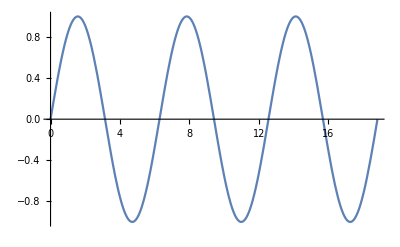

Plot3D::argrx: 调用 Plot3D 时使用了 2 个参数；应该用 3 个参数.

```mathematica
Plot[Sin[x],{x,0,6Pi}]
```

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},Mesh->Automatic,MeshFunctions->{#3&}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},Mesh->All,MeshFunctions->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Im[ArcSin[(x+I y)^4]],{x,-2,2},{y,-2,2},Mesh->None,PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]],ExclusionsStyle->{None,Red}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^4+y^4+z^4-(x^2+y^2+z^2)^2+3(x^2+y^2+z^2)==3,{x, -2,2}, {y, -2, 2}, {z, -2, 2},Mesh->None,ContourStyle->Directive[Orange,Opacity[0.8],Specularity[White,30]]]
```

-Graphics3D-

```mathematica
DensityPlot3D[x y z,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

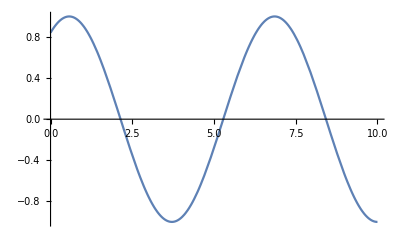
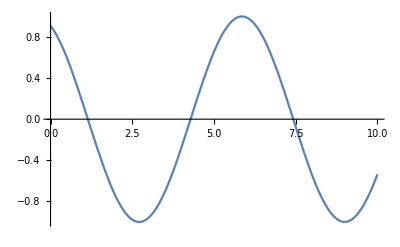
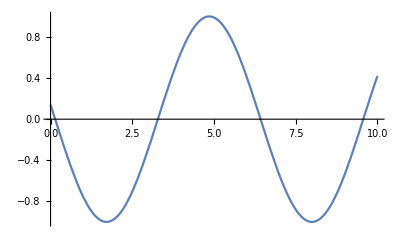
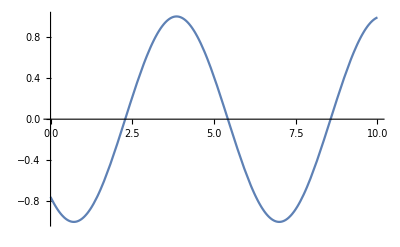
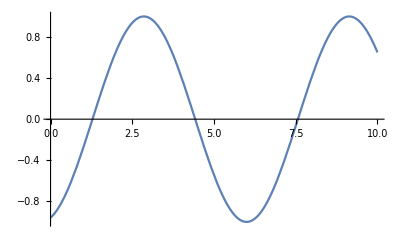

```mathematica
plots=Table[Plot[Sin[a+x],{x,0,10}],{a,5}]
```

```mathematica
ListAnimate[plots]
```

```mathematica
Export["animate.avi",plots]
```

animate.avi

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["animate.avi"]]]
```

```mathematica
Export["animate.gif",plots]
```

animate.gif

```mathematica
m=Manipulate[Plot3D[Sin[x y+a],{x,0,6},{y,0,6}],{a,0,4}]
```

```mathematica
Export["manipulate.gif",%]
```

manipulate.gif

```mathematica
Export["manipulate.gif",%]
```

manipulate.gif